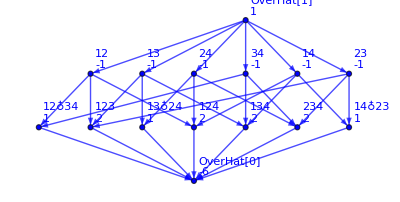

```mathematica
mob4=Graph[MobiusGraph5[K4Key,allGraphs4],VertexStyle->Blue,EdgeStyle->Blue]
```

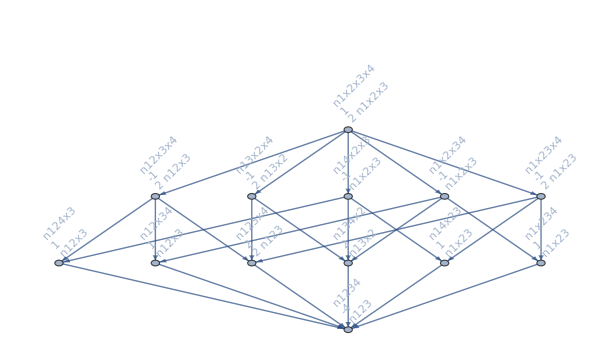

```mathematica
MobiusGraph4[361,allGraphs4]
```

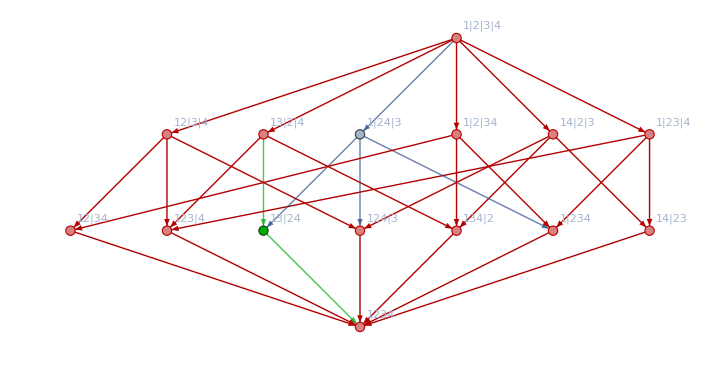

```mathematica
SummaryPrintGreen[361]
```

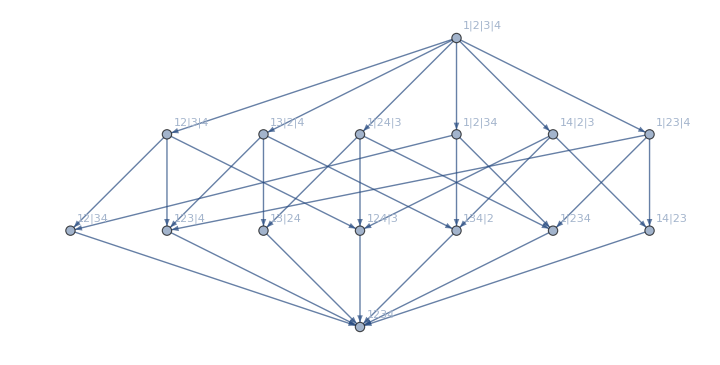
-Graphics-361-Graphics--4 n1234+2 n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4x^4-5 x^3+8 x^2-4 x
(x-2)^2 (x-1) x
 *  * 00648180
-Graphics-+-Graphics-

```mathematica
SummaryPrintGood[361]
```

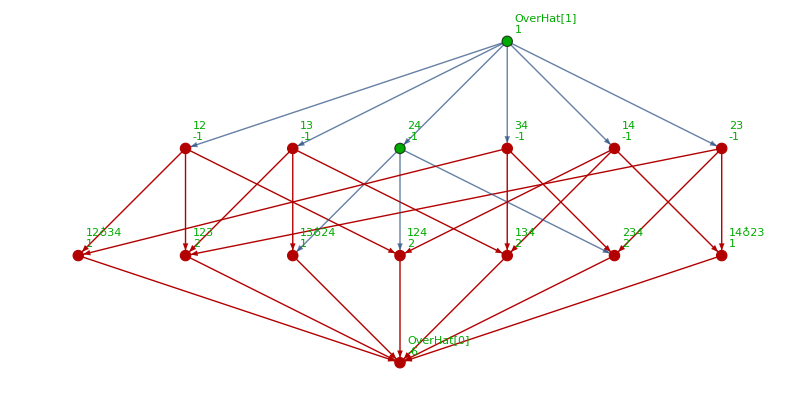
-Graphics-→-Graphics-

```mathematica
ShowDamage[allGraphs4,361]
```

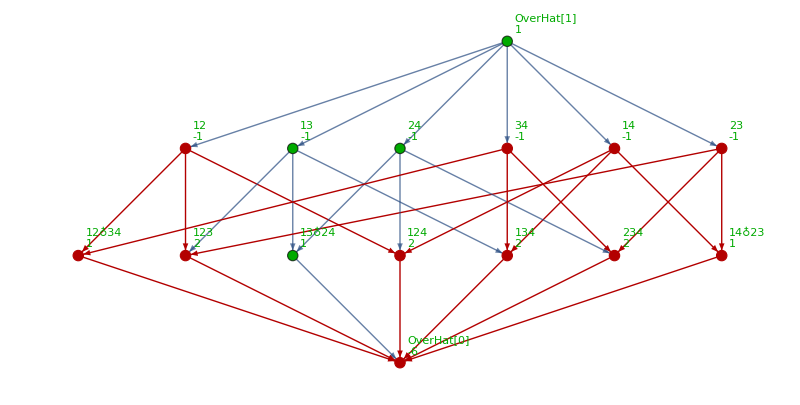
-Graphics-→-Graphics-

```mathematica
ShowDamage[allGraphs4,280]
```

```mathematica
With[{key=361},
With[
{g=MobiusGraph5[key,allGraphs4]},
allGraphs4[key,"graph"]->
Labeled[
Graph[mob4,GraphHighlight->Join[VertexList[g],EdgeList[g]], ImageSize->400
],
allGraphs4[key,"colofour"]
]
]
]
```

-Graphics-→-Graphics-v1x24x3+v1x2x3x4

```mathematica
Graph[{1,2,3,4},{Null,{{1,2},{1,3},{1,4},{2,3},{3,4}}},{EdgeStyle->{RGBColor[0,4/9,0]},ImageSize->{50,50},VertexCoordinates->{{0.,1.},{1.,0.},{0.,-1.},{-1.,0.}},VertexLabels->{3->"3",4->"4",2->"2",1->"1"},VertexSize->{0.1},VertexStyle->{RGBColor[1,0,0]}}]/.%329
```

-Graphics-v1x24x3+v1x2x3x4

```mathematica
allGraphs4[0,"colofour"]
```

v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4

```mathematica
ListofVars[allGraphs4[0,"colofour"]]
```

{v1234,v123x4,v124x3,v12x34,v12x3x4,v134x2,v13x24,v13x2x4,v14x23,v14x2x3,v1x234,v1x23x4,v1x24x3,v1x2x34,v1x2x3x4}

```mathematica
Sort[ListofVars[allGraphs4[0,"colofour"]],CompareSymbols]
```

{v1x2x3x4,v1x2x34,v1x23x4,v1x24x3,v12x3x4,v13x2x4,v14x2x3,v1x234,v12x34,v123x4,v124x3,v13x24,v134x2,v14x23,v1234}

```mathematica
Clarify[without_,with_,contract_]:=Block[{
all=Sort[ListofVars[allGraphs4[0,"colofour"]],CompareSymbols],
withoutv=ListofVars[allGraphs4[without,"colofour"]],
withv=ListofVars[allGraphs4[with,"colofour"]],
contractv=ListofVars[allGraphs4[contract,"colofour"]],
vars

},
TableForm[
{all,
withoutv,
withv,
contractv,
Table[
vars={Bold};
If[MemberQ[withoutv,k],vars=Append[vars,Underlined]];
If[MemberQ[withv,k],vars=Append[vars,FontSize->20]];
If[MemberQ[contractv,k],vars=Append[vars,Red]];
If[vars=={},vars=Plain];
Style[SymbolToLabel[k],vars
],
{k,all}
]
}]
]
```

```mathematica
Clarify[280,361,442]
```

v1x2x3x4 | v1x2x34 | v1x23x4 | v1x24x3 | v12x3x4 | v13x2x4 | v14x2x3 | v1x234 | v12x34 | v123x4 | v124x3 | v13x24 | v134x2 | v14x23 | v1234
v13x24 | v13x2x4 | v1x24x3 | v1x2x3x4 |  |  |  |  |  |  |  |  |  |  | 
v1x24x3 | v1x2x3x4 |  |  |  |  |  |  |  |  |  |  |  |  | 
v13x24 | v13x2x4 |  |  |  |  |  |  |  |  |  |  |  |  | 
1♁2♁3♁4 | 1♁2♁34 | 1♁23♁4 | 1♁24♁3 | 12♁3♁4 | 13♁2♁4 | 14♁2♁3 | 1♁234 | 12♁34 | 123♁4 | 124♁3 | 13♁24 | 134♁2 | 14♁23 | 1234

```mathematica
Clarify2[without_,with_,contract_]:=Block[{
all=Sort[ListofVars[allGraphs4[K4Key,"colofourrealnull"]],CompareSymbols],
withoutv=ListofVars[allGraphs4[without,"colofourrealnull"]],
withv=ListofVars[allGraphs4[with,"colofourrealnull"]],
contractv=ListofVars[allGraphs4[contract,"colofourrealnull"]],
vars

},
TableForm[
{all,
withoutv,
withv,
contractv,
Table[
vars={Bold};
If[MemberQ[withoutv,k],vars=Append[vars,Underlined]];
If[MemberQ[withv,k],vars=Append[vars,FontSize->20]];
If[MemberQ[contractv,k],vars=Append[vars,Red]];
If[vars=={},vars=Plain];
Style[SymbolToLabel[k],vars
],
{k,all}
]
}
]
]
```

```mathematica
Clarify2[280,361,442]
```

n1x2x3x4 | n1x2x34 | n1x23x4 | n1x24x3 | n12x3x4 | n13x2x4 | n14x2x3 | n1x234 | n12x34 | n123x4 | n124x3 | n13x24 | n134x2 | n14x23 | n1234
n123x4 | n124x3 | n12x34 | n134x2 | n14x23 | n1x234 | n1x2x3x4 | n1234 | n12x3x4 | n14x2x3 | n1x23x4 | n1x2x34 |  |  | 
n124x3 | n12x34 | n14x23 | n1x234 | n1x2x3x4 | n1234 | n123x4 | n12x3x4 | n134x2 | n13x2x4 | n14x2x3 | n1x23x4 | n1x2x34 |  | 
n1234 | n13x2x4 | n123x4 | n134x2 |  |  |  |  |  |  |  |  |  |  | 
1♁2♁3♁4 | 1♁2♁34 | 1♁23♁4 | 1♁24♁3 | 12♁3♁4 | 13♁2♁4 | 14♁2♁3 | 1♁234 | 12♁34 | 123♁4 | 124♁3 | 13♁24 | 134♁2 | 14♁23 | 1234

```mathematica
With[
{key=280},
Table[
{ShowGraph[allGraphs4,key],ShowGraph[allGraphs4,child[[1]]] , ShowGraph[allGraphs4,child[[2]]] }->Clarify[key,child[[1]],child[[2]]],
{child,allGraphs4[key,"children"]}
]
]
```

{{-Graphics-280,-Graphics-361,-Graphics-442}→v1x2x3x4 | v1x2x34 | v1x23x4 | v1x24x3 | v12x3x4 | v13x2x4 | v14x2x3 | v1x234 | v12x34 | v123x4 | v124x3 | v13x24 | v134x2 | v14x23 | v1234
v13x24 | v13x2x4 | v1x24x3 | v1x2x3x4 |  |  |  |  |  |  |  |  |  |  | 
v1x24x3 | v1x2x3x4 |  |  |  |  |  |  |  |  |  |  |  |  | 
v13x24 | v13x2x4 |  |  |  |  |  |  |  |  |  |  |  |  | 
1♁2♁3♁4 | 1♁2♁34 | 1♁23♁4 | 1♁24♁3 | 12♁3♁4 | 13♁2♁4 | 14♁2♁3 | 1♁234 | 12♁34 | 123♁4 | 124♁3 | 13♁24 | 134♁2 | 14♁23 | 1234,{-Graphics-280,-Graphics-283,-Graphics-286}→v1x2x3x4 | v1x2x34 | v1x23x4 | v1x24x3 | v12x3x4 | v13x2x4 | v14x2x3 | v1x234 | v12x34 | v123x4 | v124x3 | v13x24 | v134x2 | v14x23 | v1234
v13x24 | v13x2x4 | v1x24x3 | v1x2x3x4 |  |  |  |  |  |  |  |  |  |  | 
v13x2x4 | v1x2x3x4 |  |  |  |  |  |  |  |  |  |  |  |  | 
v13x24 | v1x24x3 |  |  |  |  |  |  |  |  |  |  |  |  | 
1♁2♁3♁4 | 1♁2♁34 | 1♁23♁4 | 1♁24♁3 | 12♁3♁4 | 13♁2♁4 | 14♁2♁3 | 1♁234 | 12♁34 | 123♁4 | 124♁3 | 13♁24 | 134♁2 | 14♁23 | 1234}

## Now with 5 nodes

```mathematica
Clarify5[without_,with_,contract_]:=Block[{
all,
withoutv=ListofVars[allGraphs5[without,"colofour"]],
withv=ListofVars[allGraphs5[with,"colofour"]],
contractv=ListofVars[allGraphs5[contract,"colofour"]],
vars

},
all=Sort[DeleteDuplicates[Join[withoutv,withv,contractv]],CompareSymbols];
TableForm[
Table[
vars={Bold};
If[MemberQ[withoutv,k],vars=Append[vars,Underlined]];
If[MemberQ[withv,k],vars=Append[vars,FontSize->20]];
If[MemberQ[contractv,k],vars=Append[vars,Red]];
If[vars=={},vars=Plain];
Style[SymbolToLabel[k],vars
],
{k,all}
],TableDirections->Column]
]
```

```mathematica
TableForm[With[
{key=FromDigits[{1,1,1,1,0,1},3]},
Table[
{ShowGraph[allGraphs5,key],ShowGraph[allGraphs5,child[[1]]] , ShowGraph[allGraphs5,child[[2]]]}->Framed[Clarify5[key,child[[1]],child[[2]]]],
{child,allGraphs5[key,"children"]}
]
]]
```

{-Graphics-361,-Graphics-20044,-Graphics-49204}→1♁2♁3♁4♁5
1♁2♁35♁4
12♁3♁4♁5
13♁2♁4♁5
14♁2♁3♁5
15♁2♁3♁4
12♁35♁4
135♁2♁4
14♁2♁35
{-Graphics-361,-Graphics-6922,-Graphics-35353}→1♁2♁3♁4♁5
1♁2♁35♁4
12♁3♁4♁5
13♁2♁4♁5
14♁2♁3♁5
15♁2♁3♁4
12♁35♁4
135♁2♁4
14♁2♁35
{-Graphics-361,-Graphics-2548,-Graphics-31708}→1♁2♁3♁4♁5
1♁2♁35♁4
12♁3♁4♁5
13♁2♁4♁5
14♁2♁3♁5
15♁2♁3♁4
12♁35♁4
135♁2♁4
14♁2♁35
{-Graphics-361,-Graphics-1090,-Graphics-23689}→1♁2♁3♁4♁5
1♁2♁35♁4
12♁3♁4♁5
13♁2♁4♁5
14♁2♁3♁5
15♁2♁3♁4
12♁35♁4
135♁2♁4
14♁2♁35
{-Graphics-361,-Graphics-364,-Graphics-367}→1♁2♁3♁4♁5
1♁2♁35♁4
12♁3♁4♁5
13♁2♁4♁5
14♁2♁3♁5
15♁2♁3♁4
12♁35♁4
135♁2♁4
14♁2♁35

```mathematica
Table[Labeled[allGraphs5[k,"graph"],k],{k,Select[Keys[allGraphs5],IsomorphicGraphQ[allGraphs5[#,"graph"],
Graph[{1,2,3,4,5},{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,4],UndirectedEdge[4,5],UndirectedEdge[1,5],UndirectedEdge[1,3],UndirectedEdge[1,4]}]]&]}]
```

{-Graphics-29487,-Graphics-29485,-Graphics-29439,-Graphics-29431,-Graphics-29413,-Graphics-29407,-Graphics-29277,-Graphics-29271,-Graphics-29253,-Graphics-29245,-Graphics-29199,-Graphics-29197,-Graphics-28785,-Graphics-28783,-Graphics-28713,-Graphics-28687,-Graphics-28549,-Graphics-28525,-Graphics-27333,-Graphics-27325,-Graphics-27309,-Graphics-27229,-Graphics-27085,-Graphics-27013,-Graphics-26605,-Graphics-26599,-Graphics-26581,-Graphics-26527,-Graphics-22959,-Graphics-22953,-Graphics-22933,-Graphics-22873,-Graphics-22693,-Graphics-22639,-Graphics-22233,-Graphics-22225,-Graphics-22207,-Graphics-21991,-Graphics-20775,-Graphics-20773,-Graphics-20695,-Graphics-20533,-Graphics-9813,-Graphics-9811,-Graphics-9759,-Graphics-9751,-Graphics-9595,-Graphics-9589,-Graphics-9111,-Graphics-9109,-Graphics-9031,-Graphics-8869,-Graphics-7653,-Graphics-7645,-Graphics-7627,-Graphics-7411,-Graphics-3277,-Graphics-3271,-Graphics-3253,-Graphics-3199}

```mathematica
TableForm[With[
{key=7653},
Table[
{ShowGraph[allGraphs5,key],ShowGraph[allGraphs5,child[[1]]] , ShowGraph[allGraphs5,child[[2]]]}->Framed[Clarify5[key,child[[1]],child[[2]]]],
{child,allGraphs5[key,"children"]}
]
]]
```

{-Graphics-7653,-Graphics-27336,-Graphics-49206}→1♁2♁3♁4♁5
1♁2♁3♁45
12♁3♁4♁5
14♁2♁3♁5
12♁3♁45
{-Graphics-7653,-Graphics-9840,-Graphics-31711}→1♁2♁3♁4♁5
1♁2♁3♁45
12♁3♁4♁5
14♁2♁3♁5
12♁3♁45
{-Graphics-7653,-Graphics-7654,-Graphics-9842}→1♁2♁3♁4♁5
1♁2♁3♁45
12♁3♁4♁5
14♁2♁3♁5
12♁3♁45

```mathematica
BaseGenerators[FindFullFormula[CompleteGraph[{4,4}]]]
```

<|2→{n1234x5678}|>

```mathematica
BaseGenerators[FindFullFormula[CompleteGraph[4]]]
```

<|4→{n1x2x3x4}|>

```mathematica
BaseGenerators[FindFullFormula[CompleteGraph[{3,4}]]]
```

<|2→{n123x4567}|>

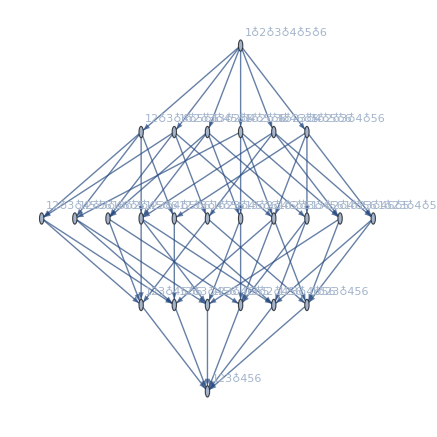

```mathematica
FormulaGraph[FindFullFormula[CompleteGraph[{3,3}]]]
```

```mathematica
BeautyGenerators[form_]:=Block[{gen=BaseGenerators[form],gen2=Association[]},
Table[
gen2[key]=Map[SymbolToLabel2[#]&,gen[key]]
,
{key,Keys[gen]}
];
gen2
]
```

```mathematica
Clarify5Bis[without_,with_,contract_]:=Block[{
withoutv=allGraphs5[without,"colofour"],
withv=allGraphs5[with,"colofour"],
contractv=allGraphs5[contract,"colofour"]

},
TableForm[
{
BeautyGenerators[withoutv],

BeautyGenerators[withv],

BeautyGenerators[contractv]
},TableDirections->Column]
]
```

```mathematica
TableForm[With[
{key=29413},
Table[
{allGraphs5[key,"graph"],allGraphs5[child[[1]],"graph"],allGraphs5[child[[2]],"graph"]}->Framed[Clarify5Bis[key,child[[1]],child[[2]]]],
{child,allGraphs5[key,"children"]}
]
]]
```

{-Graphics-,-Graphics-,-Graphics-}→<|3→{24♁35},4→{25}|>
<|4→{35,25}|>
<|3→{24♁35}|>
{-Graphics-,-Graphics-,-Graphics-}→<|3→{24♁35},4→{25}|>
<|3→{24♁35}|>
<|4→{25}|>
{-Graphics-,-Graphics-,-Graphics-}→<|3→{24♁35},4→{25}|>
<|4→{25,24}|>
<|3→{24♁35}|>

```mathematica
TableForm[With[
{key=7653},
Table[
{allGraphs5[key,"graph"],allGraphs5[child[[1]],"graph"],allGraphs5[child[[2]],"graph"]}->Framed[Clarify5Bis[key,child[[1]],child[[2]]]],
{child,allGraphs5[key,"children"]}
]
]]
```

{-Graphics-,-Graphics-,-Graphics-}→<|3→{12♁45},4→{14}|>
<|4→{45,14}|>
<|3→{12♁45}|>
{-Graphics-,-Graphics-,-Graphics-}→<|3→{12♁45},4→{14}|>
<|3→{12♁45}|>
<|4→{14}|>
{-Graphics-,-Graphics-,-Graphics-}→<|3→{12♁45},4→{14}|>
<|4→{14,12}|>
<|3→{12♁45}|>

## Now with 6 nodes

```mathematica
Clarify6[without_,with_,contract_]:=Block[{
all,
withoutv=ListofVars[allGraphs6[without,"colofour"]],
withv=ListofVars[allGraphs6[with,"colofour"]],
contractv=ListofVars[allGraphs6[contract,"colofour"]],
vars

},
all=Sort[DeleteDuplicates[Join[withoutv,withv,contractv]],CompareSymbols];
TableForm[
Table[
vars={Bold};
If[MemberQ[withoutv,k],vars=Append[vars,Underlined]];
If[MemberQ[withv,k],vars=Append[vars,FontSize->20]];
If[MemberQ[contractv,k],vars=Append[vars,Red]];
If[vars=={},vars=Plain];
Style[SymbolToLabel[k],vars
],
{k,all}
],TableDirections->Column]
]
```

```mathematica
TableForm[With[
{key=FromDigits[{1,1,1,1,0,1},3]},
Table[
{ShowGraph[allGraphs6,key],ShowGraph[allGraphs6,child[[1]]] , ShowGraph[allGraphs6,child[[2]]]}->Framed[Clarify6[key,child[[1]],child[[2]]]],
{child,allGraphs5[key,"children"]}
]
]]
```

{-Graphics-361,-Graphics-20044,-Graphics-49204}→1♁2♁3♁4♁5♁6
1♁2♁3♁46♁5
1♁23♁4♁5♁6
1♁24♁3♁5♁6
1♁25♁3♁4♁6
1♁26♁3♁4♁5
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁46♁5
1♁246♁3♁5
1♁25♁3♁46
12♁3♁46♁5
123♁4♁5♁6
124♁3♁5♁6
125♁3♁4♁6
126♁3♁4♁5
13♁2♁46♁5
13♁24♁5♁6
13♁25♁4♁6
13♁26♁4♁5
14♁23♁5♁6
14♁25♁3♁6
14♁26♁3♁5
146♁2♁3♁5
15♁2♁3♁46
15♁23♁4♁6
15♁24♁3♁6
15♁26♁3♁4
16♁23♁4♁5
16♁24♁3♁5
16♁25♁3♁4
123♁46♁5
1246♁3♁5
125♁3♁46
13♁246♁5
13♁25♁46
146♁23♁5
146♁25♁3
15♁23♁46
15♁246♁3
{-Graphics-361,-Graphics-6922,-Graphics-35353}→1♁2♁3♁4♁5♁6
1♁2♁3♁46♁5
1♁23♁4♁5♁6
1♁24♁3♁5♁6
1♁25♁3♁4♁6
1♁26♁3♁4♁5
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁46♁5
1♁246♁3♁5
1♁25♁3♁46
12♁3♁46♁5
123♁4♁5♁6
124♁3♁5♁6
125♁3♁4♁6
126♁3♁4♁5
13♁2♁46♁5
13♁24♁5♁6
13♁25♁4♁6
13♁26♁4♁5
14♁23♁5♁6
14♁25♁3♁6
14♁26♁3♁5
146♁2♁3♁5
15♁2♁3♁46
15♁23♁4♁6
15♁24♁3♁6
15♁26♁3♁4
16♁23♁4♁5
16♁24♁3♁5
16♁25♁3♁4
123♁46♁5
1246♁3♁5
125♁3♁46
13♁246♁5
13♁25♁46
146♁23♁5
146♁25♁3
15♁23♁46
15♁246♁3
{-Graphics-361,-Graphics-2548,-Graphics-31708}→1♁2♁3♁4♁5♁6
1♁2♁3♁46♁5
1♁23♁4♁5♁6
1♁24♁3♁5♁6
1♁25♁3♁4♁6
1♁26♁3♁4♁5
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁46♁5
1♁246♁3♁5
1♁25♁3♁46
12♁3♁46♁5
123♁4♁5♁6
124♁3♁5♁6
125♁3♁4♁6
126♁3♁4♁5
13♁2♁46♁5
13♁24♁5♁6
13♁25♁4♁6
13♁26♁4♁5
14♁23♁5♁6
14♁25♁3♁6
14♁26♁3♁5
146♁2♁3♁5
15♁2♁3♁46
15♁23♁4♁6
15♁24♁3♁6
15♁26♁3♁4
16♁23♁4♁5
16♁24♁3♁5
16♁25♁3♁4
123♁46♁5
1246♁3♁5
125♁3♁46
13♁246♁5
13♁25♁46
146♁23♁5
146♁25♁3
15♁23♁46
15♁246♁3
{-Graphics-361,-Graphics-1090,-Graphics-23689}→1♁2♁3♁4♁5♁6
1♁2♁3♁46♁5
1♁23♁4♁5♁6
1♁24♁3♁5♁6
1♁25♁3♁4♁6
1♁26♁3♁4♁5
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁46♁5
1♁246♁3♁5
1♁25♁3♁46
12♁3♁46♁5
123♁4♁5♁6
124♁3♁5♁6
125♁3♁4♁6
126♁3♁4♁5
13♁2♁46♁5
13♁24♁5♁6
13♁25♁4♁6
13♁26♁4♁5
14♁23♁5♁6
14♁25♁3♁6
14♁26♁3♁5
146♁2♁3♁5
15♁2♁3♁46
15♁23♁4♁6
15♁24♁3♁6
15♁26♁3♁4
16♁23♁4♁5
16♁24♁3♁5
16♁25♁3♁4
123♁46♁5
1246♁3♁5
125♁3♁46
13♁246♁5
13♁25♁46
146♁23♁5
146♁25♁3
15♁23♁46
15♁246♁3
{-Graphics-361,-Graphics-364,-Graphics-367}→1♁2♁3♁4♁5♁6
1♁2♁3♁46♁5
1♁23♁4♁5♁6
1♁24♁3♁5♁6
1♁25♁3♁4♁6
1♁26♁3♁4♁5
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁46♁5
1♁246♁3♁5
1♁25♁3♁46
12♁3♁46♁5
123♁4♁5♁6
124♁3♁5♁6
125♁3♁4♁6
126♁3♁4♁5
13♁2♁46♁5
13♁24♁5♁6
13♁25♁4♁6
13♁26♁4♁5
14♁23♁5♁6
14♁25♁3♁6
14♁26♁3♁5
146♁2♁3♁5
15♁2♁3♁46
15♁23♁4♁6
15♁24♁3♁6
15♁26♁3♁4
16♁23♁4♁5
16♁24♁3♁5
16♁25♁3♁4
123♁46♁5
1246♁3♁5
125♁3♁46
13♁246♁5
13♁25♁46
146♁23♁5
146♁25♁3
15♁23♁46
15♁246♁3

```mathematica
TableForm[With[
{key=7653},
Table[
{ShowGraph[allGraphs6,key],ShowGraph[allGraphs6,child[[1]]] , ShowGraph[allGraphs6,child[[2]]]}->Framed[Clarify6[key,child[[1]],child[[2]]]],
{child,allGraphs6[key,"children"]}
]
]]
```

{-Graphics-7653,-Graphics-4790622,-Graphics-10164081}→1♁2♁3♁4♁5♁6
1♁2♁3♁4♁56
1♁23♁4♁5♁6
1♁25♁3♁4♁6
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁4♁56
12♁3♁4♁56
123♁4♁5♁6
125♁3♁4♁6
13♁2♁4♁56
13♁25♁4♁6
14♁2♁3♁56
14♁23♁5♁6
14♁25♁3♁6
15♁23♁4♁6
156♁2♁3♁4
16♁23♁4♁5
16♁25♁3♁4
123♁4♁56
14♁23♁56
156♁23♁4
{-Graphics-7653,-Graphics-1601976,-Graphics-3963936}→1♁2♁3♁4♁5♁6
1♁2♁3♁4♁56
1♁23♁4♁5♁6
1♁25♁3♁4♁6
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁4♁56
12♁3♁4♁56
123♁4♁5♁6
125♁3♁4♁6
13♁2♁4♁56
13♁25♁4♁6
14♁2♁3♁56
14♁23♁5♁6
14♁25♁3♁6
15♁23♁4♁6
156♁2♁3♁4
16♁23♁4♁5
16♁25♁3♁4
123♁4♁56
14♁23♁56
156♁23♁4
{-Graphics-7653,-Graphics-539094,-Graphics-7684023}→1♁2♁3♁4♁5♁6
1♁2♁3♁4♁56
1♁23♁4♁5♁6
1♁25♁3♁4♁6
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁4♁56
12♁3♁4♁56
123♁4♁5♁6
125♁3♁4♁6
13♁2♁4♁56
13♁25♁4♁6
14♁2♁3♁56
14♁23♁5♁6
14♁25♁3♁6
15♁23♁4♁6
156♁2♁3♁4
16♁23♁4♁5
16♁25♁3♁4
123♁4♁56
14♁23♁56
156♁23♁4
{-Graphics-7653,-Graphics-184800,-Graphics-2487711}→1♁2♁3♁4♁5♁6
1♁2♁3♁4♁56
1♁23♁4♁5♁6
1♁25♁3♁4♁6
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁4♁56
12♁3♁4♁56
123♁4♁5♁6
125♁3♁4♁6
13♁2♁4♁56
13♁25♁4♁6
14♁2♁3♁56
14♁23♁5♁6
14♁25♁3♁6
15♁23♁4♁6
156♁2♁3♁4
16♁23♁4♁5
16♁25♁3♁4
123♁4♁56
14♁23♁56
156♁23♁4
{-Graphics-7653,-Graphics-66702,-Graphics-7034484}→1♁2♁3♁4♁5♁6
1♁2♁3♁4♁56
1♁23♁4♁5♁6
1♁25♁3♁4♁6
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁4♁56
12♁3♁4♁56
123♁4♁5♁6
125♁3♁4♁6
13♁2♁4♁56
13♁25♁4♁6
14♁2♁3♁56
14♁23♁5♁6
14♁25♁3♁6
15♁23♁4♁6
156♁2♁3♁4
16♁23♁4♁5
16♁25♁3♁4
123♁4♁56
14♁23♁56
156♁23♁4
{-Graphics-7653,-Graphics-27336,-Graphics-49206}→1♁2♁3♁4♁5♁6
1♁2♁3♁4♁56
1♁23♁4♁5♁6
1♁25♁3♁4♁6
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁4♁56
12♁3♁4♁56
123♁4♁5♁6
125♁3♁4♁6
13♁2♁4♁56
13♁25♁4♁6
14♁2♁3♁56
14♁23♁5♁6
14♁25♁3♁6
15♁23♁4♁6
156♁2♁3♁4
16♁23♁4♁5
16♁25♁3♁4
123♁4♁56
14♁23♁56
156♁23♁4
{-Graphics-7653,-Graphics-9840,-Graphics-31711}→1♁2♁3♁4♁5♁6
1♁2♁3♁4♁56
1♁23♁4♁5♁6
1♁25♁3♁4♁6
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁4♁56
12♁3♁4♁56
123♁4♁5♁6
125♁3♁4♁6
13♁2♁4♁56
13♁25♁4♁6
14♁2♁3♁56
14♁23♁5♁6
14♁25♁3♁6
15♁23♁4♁6
156♁2♁3♁4
16♁23♁4♁5
16♁25♁3♁4
123♁4♁56
14♁23♁56
156♁23♁4
{-Graphics-7653,-Graphics-7654,-Graphics-9842}→1♁2♁3♁4♁5♁6
1♁2♁3♁4♁56
1♁23♁4♁5♁6
1♁25♁3♁4♁6
12♁3♁4♁5♁6
13♁2♁4♁5♁6
14♁2♁3♁5♁6
15♁2♁3♁4♁6
16♁2♁3♁4♁5
1♁23♁4♁56
12♁3♁4♁56
123♁4♁5♁6
125♁3♁4♁6
13♁2♁4♁56
13♁25♁4♁6
14♁2♁3♁56
14♁23♁5♁6
14♁25♁3♁6
15♁23♁4♁6
156♁2♁3♁4
16♁23♁4♁5
16♁25♁3♁4
123♁4♁56
14♁23♁56
156♁23♁4

```mathematica
BaseGenerators[FindFullFormula[CompleteGraph[{4,4}]]]
```

<|2→{n1234x5678}|>

```mathematica
BaseGenerators[FindFullFormula[CompleteGraph[4]]]
```

<|4→{n1x2x3x4}|>

```mathematica
BaseGenerators[FindFullFormula[CompleteGraph[{3,4}]]]
```

<|2→{n123x4567}|>

```mathematica
FormulaGraph[FindFullFormula[CompleteGraph[{3,3}]]]
```

-Graphics-

```mathematica
BeautyGenerators[form_]:=Block[{gen=BaseGenerators[form],gen2=Association[]},
Table[
gen2[key]=Map[SymbolToLabel2[#]&,gen[key]]
,
{key,Keys[gen]}
];
gen2
]
```

```mathematica
Clarify6Bis[without_,with_,contract_]:=Block[{
withoutv=allGraphs6[without,"colofour"],
withv=allGraphs6[with,"colofour"],
contractv=allGraphs6[contract,"colofour"]

},
TableForm[
{
BeautyGenerators[withoutv],

BeautyGenerators[withv],

BeautyGenerators[contractv]
},TableDirections->Column]
]
```

```mathematica
TableForm[With[
{key=29413},
Table[
{ShowGraph[allGraphs6,key],ShowGraph[allGraphs6,child[[1]]] , ShowGraph[allGraphs6,child[[2]]]}->Framed[Clarify6Bis[key,child[[1]],child[[2]]]],
{child,allGraphs6[key,"children"]}
]
]]
```

{-Graphics-29413,-Graphics-4812382,-Graphics-11957311}→<|3→{146♁35,135♁46,12♁35♁46},4→{15♁36,14♁36,136,12♁36}|>
<|3→{146♁35,135♁46},4→{15♁36,14♁36,136}|>
<|3→{12♁35♁46},4→{12♁36}|>
{-Graphics-29413,-Graphics-1623736,-Graphics-8532469}→<|3→{146♁35,135♁46,12♁35♁46},4→{15♁36,14♁36,136,12♁36}|>
<|3→{146♁35,12♁35♁46},4→{15♁46,15♁36,14♁36,12♁36}|>
<|3→{135♁46},4→{136}|>
{-Graphics-29413,-Graphics-560854,-Graphics-7646734}→<|3→{146♁35,135♁46,12♁35♁46},4→{15♁36,14♁36,136,12♁36}|>
<|3→{135♁46,12♁35♁46},4→{16♁35,15♁36,136,12♁36}|>
<|3→{146♁35},4→{14♁36}|>
{-Graphics-29413,-Graphics-206560,-Graphics-5757166}→<|3→{146♁35,135♁46,12♁35♁46},4→{15♁36,14♁36,136,12♁36}|>
<|3→{146♁35,12♁35♁46},4→{14♁36,13♁46,136,12♁36}|>
<|3→{135♁46},4→{15♁36}|>
{-Graphics-29413,-Graphics-88462,-Graphics-5107627}→<|3→{146♁35,135♁46,12♁35♁46},4→{15♁36,14♁36,136,12♁36}|>
<|3→{135♁46,12♁35♁46},4→{15♁36,14♁36,14♁35,12♁36}|>
<|3→{146♁35},4→{136}|>
{-Graphics-29413,-Graphics-29494,-Graphics-29602}→<|3→{146♁35,135♁46,12♁35♁46},4→{15♁36,14♁36,136,12♁36}|>
<|4→{15♁46,15♁36,14♁36,146,13♁46,136,12♁46,12♁36}|>
<|3→{146♁35,135♁46,12♁35♁46}|>
{-Graphics-29413,-Graphics-29440,-Graphics-29551}→<|3→{146♁35,135♁46,12♁35♁46},4→{15♁36,14♁36,136,12♁36}|>
<|3→{146♁35,135♁46,12♁35♁46}|>
<|4→{15♁36,14♁36,136,12♁36}|>
{-Graphics-29413,-Graphics-29416,-Graphics-29446}→<|3→{146♁35,135♁46,12♁35♁46},4→{15♁36,14♁36,136,12♁36}|>
<|4→{16♁35,15♁36,14♁36,14♁35,136,135,12♁36,12♁35}|>
<|3→{146♁35,135♁46,12♁35♁46}|>

```mathematica
Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},
!EdgeQ[g,1<->2]&&
VertexCount[g]==6&&
MaximalPlanarQ[EdgeAdd[g,1<->2]]
]&]
```

{2391447,2391445,2391399,2391391,2391373,2391367,2391237,2391231,2391213,2391205,2391159,2391157,2390745,2390743,2390673,2390647,2390509,2390485,2389293,2389285,2389269,2389189,2389045,2388973,2388565,2388559,2388541,2388487,2384919,2384913,2384893,2384833,2384653,2384599,2384193,2384185,2384167,2383951,2382735,2382733,2382655,2382493,2371773,2371771,2371719,2371711,2371555,2371549,2371071,2371069,2370991,2370829,2369613,2369605,2369587,2369371,2365237,2365231,2365213,2365159,2332425,2332423,2332353,2332327,2332189,2332165,2330247,2330005,2329519,2325871,2325793,2325145,2312743,2312725,2312023,2214333,2214325,2214309,2214229,2214085,2214013,2213607,2213365,2211421,2207767,2207749,2205589,2194651,2194573,2192467,2155285,2155279,2155261,2155207,2154559,2153101,1860039,1860033,1860013,1859953,1859773,1859719,1859311,1859233,1857847,1857829,1852753,1851295,1840359,1840117,1833799,1800993,1800985,1800967,1800751,1800265,1794433,1682895,1682893,1682815,1682653,1680709,1676335,797133,797131,797079,797071,796915,796909,796423,796405,794971,794893,790599,790357,776749,775291,770917,738111,738109,738031,737869,737383,718429,620013,620005,619987,619771,617827,600331,265717,265711,265693,265639,259159,246037}

```mathematica
TableForm[With[
{key=2391445},
Table[
{ShowGraph[allGraphs6,key],ShowGraph[allGraphs6,child[[1]]], ShowGraph[allGraphs6,child[[2]]]}->Framed[Clarify6Bis[key,child[[1]],child[[2]]]],
{child,allGraphs6[key,"children"]}
]
]]
```

{-Graphics-2391445,-Graphics-7174414,-Graphics-11957383}→<|3→{12♁36♁45},4→{12♁46}|>
<|4→{36♁45},5→{46}|>
<|3→{12♁36♁45},4→{12♁46}|>
{-Graphics-2391445,-Graphics-2391472,-Graphics-2391502}→<|3→{12♁36♁45},4→{12♁46}|>
<|4→{12♁46,12♁45}|>
<|3→{12♁36♁45}|>
{-Graphics-2391445,-Graphics-2391454,-Graphics-2391466}→<|3→{12♁36♁45},4→{12♁46}|>
<|4→{12♁46,12♁36}|>
<|3→{12♁36♁45}|>
{-Graphics-2391445,-Graphics-2391448,-Graphics-2391487}→<|3→{12♁36♁45},4→{12♁46}|>
<|3→{12♁36♁45}|>
<|4→{12♁46}|>

```mathematica
FlatGenerators[form_]:=With[{all=BaseGenerators[form]},
Flatten[Join[Table[all[key],{key,Keys[all]}]]]
]
```

```mathematica
FlatGenerators[allGraphs6[360,"colofour"]]
```

{n15x246x3,n15x23x46,n156x24x3,n156x23x4,n14x256x3,n14x23x56,n146x25x3,n146x23x5,n13x25x46,n13x256x4,n13x24x56,n13x246x5,n125x3x46,n1256x3x4,n124x3x56,n1246x3x5,n123x4x56,n123x46x5}

```mathematica
TableForm[
Select[
Sort[
Table[
ShowGraph[allGraphs4,k]->FlatGenerators[allGraphs4[k,"colofour"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],
Length[#1[[2]]]>Length[#2[[2]]]&
],
Length[#[[2]]]==1&
]
]
```

-Graphics-31→{n123x4}
-Graphics-91→{n124x3}
-Graphics-121→{n12x3x4}
-Graphics-120→{n12x34}
-Graphics-255→{n134x2}
-Graphics-280→{n13x24}
-Graphics-283→{n13x2x4}
-Graphics-328→{n14x23}
-Graphics-337→{n14x2x3}
-Graphics-355→{n1x23x4}
-Graphics-361→{n1x24x3}
-Graphics-364→{n1x2x3x4}
-Graphics-363→{n1x2x34}
-Graphics-351→{n1x234}
-Graphics-0→{n1234}

```mathematica
Monitor[Table[allGraphs5[k,"generators"]=FlatGenerators[allGraphs5[k,"colofour"]],{k,Sort[Keys[allGraphs5]]}],k]
```

{{n12345},{n15x234,n14x235,n135x24,n134x25,n125x34,n124x35,n1235x4,n1234x5},{n12345},{n15x234,n145x23,n13x245,n134x25,n125x34,n1245x3,n123x45,n1234x5},{n15x234,n134x25,n125x34,n1234x5},{n12345},{n14x235,n145x23,n13x245,n135x24,n124x35,n1245x3,n123x45,n1235x4},{n14x235,n135x24,n124x35,n1235x4},{n145x23,n13x245,n1245x3,n123x45},{n15x24x3,n15x23x4,n14x25x3,n14x23x5,n13x25x4,n13x24x5,n125x3x4,n124x3x5,n123x4x5},{n145x23,n13x245,n1245x3,n123x45},{n14x235,n135x24,n124x35,n1235x4},{n12345},{n15x234,n134x25,n125x34,n1234x5},{n12345},1865,{n12345},{n1235x4,n1234x5},{n12345},{n123x45,n1234x5},{n1234x5},{n12345},{n123x45,n1235x4},{n1235x4},{n123x45},{n123x4x5},{n123x45},{n1235x4},{n12345},{n1234x5},{n12345}}
 |  |  |  |

```mathematica
Sort[Tally[Table[
k,{k,Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[k,"generators"]]]==1&]}],allGraphs5[#1,"generators"]==allGraphs5[#2,"generators"]&],#1[[2]]<#2[[2]]&]
```

{{1,1},{3,1},{13,1},{9,1},{63,1},{45,1},{37,1},{40,1},{39,1},{36,1},{27,1},{165,1},{87,1},{85,1},{84,1},{94,1},{93,1},{109,1},{112,1},{111,1},{118,1},{117,1},{81,1},{487,1},{245,1},{244,1},{247,1},{253,1},{256,1},{271,1},{274,1},{273,1},{282,1},{279,1},{325,1},{327,1},{334,1},{336,1},{333,1},{352,1},{354,1},{364,1},{360,1},{243,1},{1467,1},{1539,1},{1791,1},{1701,1},{747,1},{739,1},{742,1},{741,1},{738,1},{766,1},{769,1},{768,1},{765,1},{891,1},{811,1},{814,1},{813,1},{820,1},{823,1},{822,1},{819,1},{838,1},{841,1},{840,1},{847,1},{846,1},{837,1},{810,1},{1395,1},{1306,1},{1305,1},{1215,1},{973,1},{976,1},{975,1},{982,1},{985,1},{984,1},{981,1},{1000,1},{1003,1},{1002,1},{1011,1},{1008,1},{999,1},{1146,1},{1143,1},{1054,1},{1056,1},{1071,1},{1063,1},{1066,1},{1065,1},{1062,1},{1081,1},{1083,1},{1098,1},{1090,1},{1093,1},{1092,1},{1089,1},{1080,1},{1053,1},{972,1},{729,1},{4377,1},{4401,1},{4647,1},{4617,1},{6077,1},{5350,1},{5377,1},{5374,1},{5347,1},{2193,1},{2191,1},{2190,1},{2200,1},{2199,1},{2241,1},{2215,1},{2218,1},{2217,1},{2224,1},{2227,1},{2226,1},{2223,1},{2214,1},{2272,1},{2271,1},{2281,1},{2280,1},{2296,1},{2299,1},{2298,1},{2305,1},{2304,1},{2295,1},{2733,1},{2704,1},{2703,1},{2673,1},{2431,1},{2434,1},{2433,1},{2440,1},{2443,1},{2442,1},{2439,1},{2496,1},{2487,1},{2458,1},{2463,1},{2461,1},{2460,1},{2470,1},{2469,1},{2466,1},{2457,1},{2512,1},{2514,1},{2521,1},{2523,1},{2520,1},{2539,1},{2544,1},{2542,1},{2541,1},{2551,1},{2550,1},{2547,1},{2538,1},{2511,1},{2430,1},{3898,1},{3979,1},{3970,1},{3889,1},{2917,1},{2920,1},{2919,1},{2926,1},{2925,1},{2944,1},{2947,1},{2946,1},{2953,1},{2952,1},{2943,1},{2998,1},{3001,1},{3000,1},{3007,1},{3006,1},{2997,1},{3403,1},{3433,1},{3432,1},{3493,1},{3492,1},{3161,1},{3160,1},{3163,1},{3162,1},{3169,1},{3172,1},{3168,1},{3187,1},{3190,1},{3189,1},{3196,1},{3199,1},{3198,1},{3195,1},{3186,1},{3241,1},{3244,1},{3243,1},{3250,1},{3253,1},{3252,1},{3249,1},{3268,1},{3271,1},{3270,1},{3277,1},{3280,1},{3276,1},{3240,1},{3159,1},{2187,1},{13123,1},{13149,1},{13231,1},{13203,1},{14667,1},{13936,1},{13963,1},{13962,1},{13935,1},{17541,1},{15346,1},{15345,1},{15427,1},{15426,1},{6563,1},{6562,1},{6565,1},{6571,1},{6574,1},{6615,1},{6589,1},{6592,1},{6591,1},{6598,1},{6601,1},{6600,1},{6597,1},{6588,1},{6779,1},{6754,1},{6751,1},{6723,1},{6643,1},{6646,1},{6645,1},{6652,1},{6655,1},{6654,1},{6651,1},{6706,1},{6697,1},{6671,1},{6670,1},{6673,1},{6672,1},{6679,1},{6682,1},{6678,1},{6669,1},{6642,1},{6805,1},{6808,1},{6814,1},{6817,1},{6832,1},{6835,1},{6834,1},{6843,1},{6840,1},{6831,1},{6886,1},{6888,1},{6895,1},{6897,1},{6894,1},{6914,1},{6913,1},{6916,1},{6915,1},{6922,1},{6925,1},{6921,1},{6912,1},{6885,1},{8112,1},{8103,1},{8355,1},{8346,1},{7291,1},{7294,1},{7293,1},{7302,1},{7299,1},{7318,1},{7321,1},{7320,1},{7329,1},{7326,1},{7317,1},{7455,1},{7483,1},{7480,1},{7372,1},{7377,1},{7375,1},{7374,1},{7384,1},{7383,1},{7380,1},{7399,1},{7402,1},{7401,1},{7408,1},{7411,1},{7410,1},{7407,1},{7398,1},{7371,1},{7534,1},{7537,1},{7536,1},{7545,1},{7542,1},{7707,1},{7704,1},{7615,1},{7618,1},{7617,1},{7624,1},{7627,1},{7626,1},{7623,1},{7642,1},{7645,1},{7644,1},{7654,1},{7653,1},{7650,1},{7614,1},{7533,1},{10974,1},{10971,1},{11217,1},{11214,1},{8749,1},{8751,1},{8758,1},{8760,1},{8757,1},{8811,1},{8776,1},{8778,1},{8793,1},{8785,1},{8788,1},{8787,1},{8784,1},{8775,1},{8830,1},{8832,1},{8839,1},{8841,1},{8838,1},{8893,1},{8884,1},{8857,1},{8860,1},{8859,1},{8866,1},{8869,1},{8868,1},{8865,1},{8856,1},{8829,1},{8992,1},{8994,1},{9001,1},{9003,1},{9000,1},{9057,1},{9048,1},{9019,1},{9022,1},{9021,1},{9028,1},{9031,1},{9030,1},{9027,1},{9018,1},{9100,1},{9102,1},{9109,1},{9112,1},{9111,1},{9108,1},{8991,1},{9478,1},{9480,1},{9490,1},{9486,1},{9505,1},{9507,1},{9522,1},{9514,1},{9517,1},{9516,1},{9513,1},{9504,1},{9559,1},{9564,1},{9562,1},{9561,1},{9571,1},{9570,1},{9567,1},{9586,1},{9589,1},{9588,1},{9595,1},{9598,1},{9594,1},{9558,1},{9722,1},{9721,1},{9724,1},{9723,1},{9730,1},{9733,1},{9729,1},{9748,1},{9751,1},{9750,1},{9760,1},{9759,1},{9756,1},{9802,1},{9804,1},{9811,1},{9814,1},{9813,1},{9810,1},{9720,1},{6561,1},{39367,1},{39369,1},{39379,1},{39375,1},{40887,1},{40132,1},{40135,1},{40134,1},{40131,1},{43905,1},{41638,1},{41637,1},{41647,1},{41646,1},{52975,1},{46171,1},{46174,1},{46180,1},{46183,1},{19685,1},{19684,1},{19689,1},{19687,1},{19686,1},{19709,1},{19705,1},{19701,1},{19693,1},{19699,1},{19697,1},{19696,1},{19695,1},{19692,1},{19711,1},{19714,1},{19713,1},{19732,1},{19720,1},{19723,1},{19722,1},{19719,1},{19765,1},{19768,1},{19767,1},{19774,1},{19780,1},{19777,1},{19776,1},{19773,1},{19792,1},{19795,1},{19794,1},{19801,1},{19804,1},{19800,1},{19927,1},{19930,1},{19929,1},{19936,1},{19940,1},{19939,1},{19938,1},{19935,1},{19954,1},{19957,1},{19956,1},{19966,1},{19965,1},{19962,1},{20008,1},{20010,1},{20017,1},{20020,1},{20019,1},{20016,1},{20035,1},{20037,1},{20047,1},{20043,1},{21177,1},{21258,1},{21420,1},{21501,1},{20413,1},{20416,1},{20415,1},{20434,1},{20422,1},{20425,1},{20424,1},{20421,1},{20475,1},{20440,1},{20443,1},{20442,1},{20461,1},{20457,1},{20449,1},{20452,1},{20451,1},{20448,1},{20439,1},{20496,1},{20506,1},{20505,1},{20502,1},{20523,1},{20530,1},{20533,1},{20532,1},{20529,1},{20520,1},{20493,1},{20656,1},{20665,1},{20668,1},{20664,1},{20683,1},{20692,1},{20695,1},{20694,1},{20691,1},{20682,1},{20754,1},{20746,1},{20748,1},{20745,1},{20781,1},{20773,1},{20776,1},{20775,1},{20772,1},{20763,1},{20736,1},{20655,1},{24141,1},{24168,1},{24384,1},{24411,1},{21871,1},{21874,1},{21873,1},{21880,1},{21886,1},{21883,1},{21882,1},{21879,1},{21900,1},{21910,1},{21909,1},{21906,1},{21897,1},{22035,1},{21952,1},{21957,1},{21955,1},{21954,1},{21961,1},{21967,1},{21964,1},{21963,1},{21960,1},{21982,1},{21981,1},{21991,1},{21990,1},{21987,1},{21978,1},{21951,1},{22114,1},{22117,1},{22116,1},{22126,1},{22146,1},{22144,1},{22143,1},{22152,1},{22140,1},{22195,1},{22198,1},{22197,1},{22207,1},{22206,1},{22227,1},{22225,1},{22224,1},{22234,1},{22233,1},{22221,1},{22194,1},{22113,1},{22600,1},{22603,1},{22602,1},{22609,1},{22612,1},{22608,1},{22662,1},{22629,1},{22636,1},{22639,1},{22638,1},{22635,1},{22626,1},{22764,1},{22684,1},{22683,1},{22693,1},{22692,1},{22689,1},{22708,1},{22711,1},{22710,1},{22717,1},{22720,1},{22716,1},{22680,1},{22844,1},{22843,1},{22846,1},{22852,1},{22870,1},{22873,1},{22872,1},{22878,1},{22869,1},{22924,1},{22926,1},{22933,1},{22932,1},{22951,1},{22954,1},{22953,1},{22960,1},{22959,1},{22923,1},{22842,1},{33049,1},{33076,1},{33130,1},{33157,1},{26245,1},{26248,1},{26247,1},{26254,1},{26258,1},{26257,1},{26256,1},{26253,1},{26272,1},{26281,1},{26284,1},{26280,1},{26271,1},{26326,1},{26329,1},{26328,1},{26338,1},{26354,1},{26353,1},{26356,1},{26362,1},{26352,1},{26325,1},{26731,1},{26489,1},{26488,1},{26491,1},{26490,1},{26497,1},{26501,1},{26500,1},{26499,1},{26496,1},{26515,1},{26518,1},{26524,1},{26527,1},{26523,1},{26514,1},{26569,1},{26572,1},{26571,1},{26578,1},{26581,1},{26597,1},{26596,1},{26599,1},{26605,1},{26608,1},{26595,1},{26568,1},{26487,1},{26974,1},{26977,1},{26976,1},{26986,1},{26985,1},{26982,1},{27036,1},{27001,1},{27010,1},{27013,1},{27012,1},{27009,1},{27000,1},{27060,1},{27058,1},{27057,1},{27066,1},{27082,1},{27085,1},{27084,1},{27090,1},{27081,1},{27054,1},{27460,1},{27217,1},{27220,1},{27226,1},{27229,1},{27225,1},{27244,1},{27247,1},{27246,1},{27256,1},{27255,1},{27252,1},{27298,1},{27300,1},{27309,1},{27306,1},{27325,1},{27328,1},{27327,1},{27336,1},{27333,1},{27297,1},{27216,1},{28432,1},{28434,1},{28441,1},{28444,1},{28443,1},{28440,1},{28476,1},{28468,1},{28470,1},{28467,1},{28458,1},{28596,1},{28513,1},{28516,1},{28515,1},{28525,1},{28524,1},{28540,1},{28542,1},{28549,1},{28548,1},{28539,1},{28512,1},{28918,1},{28675,1},{28678,1},{28677,1},{28684,1},{28687,1},{28702,1},{28704,1},{28713,1},{28710,1},{28701,1},{28756,1},{28758,1},{28765,1},{28768,1},{28767,1},{28764,1},{28783,1},{28785,1},{28792,1},{28794,1},{28791,1},{28674,1},{29161,1},{29163,1},{29173,1},{29169,1},{29223,1},{29205,1},{29197,1},{29200,1},{29199,1},{29196,1},{29187,1},{29325,1},{29247,1},{29245,1},{29244,1},{29254,1},{29253,1},{29269,1},{29272,1},{29271,1},{29278,1},{29277,1},{29241,1},{29647,1},{29405,1},{29404,1},{29407,1},{29413,1},{29416,1},{29431,1},{29434,1},{29433,1},{29442,1},{29439,1},{29485,1},{29487,1},{29494,1},{29496,1},{29493,1},{29512,1},{29514,1},{29524,1},{29520,1},{29403,1},{19683,1},{22,2},{16,2},{12,2},{190,2},{136,2},{108,2},{516,2},{607,2},{576,2},{300,2},{270,2},{445,2},{414,2},{391,2},{373,2},{367,2},{363,2},{324,2},{2034,2},{1872,2},{1782,2},{1336,2},{1335,2},{1174,2},{1171,2},{1075,2},{1102,2},{4890,2},{4674,2},{4644,2},{5590,2},{5104,2},{2794,2},{2793,2},{2473,2},{2578,2},{2569,2},{2554,2},{4132,2},{3646,2},{3402,2},{3171,2},{3279,2},{3267,2},{2916,2},{13312,2},{13258,2},{13230,2},{14016,2},{13854,2},{15372,2},{16051,2},{16078,2},{16077,2},{16132,2},{16131,2},{15318,2},{6681,2},{7006,2},{7003,2},{6952,2},{6943,2},{6924,2},{8184,2},{8022,2},{7452,2},{7387,2},{7657,2},{7641,2},{7290,2},{10998,2},{11677,2},{11704,2},{11701,2},{11920,2},{11917,2},{10944,2},{8802,2},{8797,2},{9121,2},{9099,2},{10219,2},{10300,2},{10291,2},{10462,2},{10453,2},{9499,2},{9493,2},{9489,2},{9526,2},{9574,2},{9597,2},{9585,2},{9732,2},{9763,2},{9747,2},{9823,2},{9801,2},{8748,2},{39388,2},{39382,2},{39378,2},{40140,2},{40122,2},{41640,2},{42391,2},{42394,2},{42393,2},{42400,2},{42399,2},{41634,2},{46172,2},{46927,2},{46930,2},{46929,2},{46938,2},{46935,2},{48439,2},{48441,2},{48448,2},{48450,2},{48447,2},{49195,2},{49197,2},{49207,2},{49203,2},{46170,2},{19803,2},{19969,2},{20029,2},{20056,2},{20050,2},{20046,2},{21186,2},{21168,2},{20484,2},{20557,2},{20721,2},{20803,2},{20412,2},{24144,2},{24871,2},{24898,2},{24895,2},{25138,2},{25111,2},{24138,2},{22038,2},{22063,2},{22287,2},{22315,2},{23365,2},{23446,2},{23437,2},{23680,2},{23599,2},{22611,2},{22792,2},{22789,2},{22744,2},{22735,2},{22719,2},{22707,2},{22899,2},{23041,2},{23013,2},{22981,2},{22950,2},{21870,2},{33050,2},{33781,2},{33808,2},{33807,2},{33888,2},{33861,2},{35245,2},{35271,2},{35326,2},{35352,2},{35325,2},{35977,2},{36003,2},{36085,2},{36057,2},{33048,2},{26732,2},{26761,2},{26821,2},{26851,2},{27741,2},{27813,2},{27984,2},{28056,2},{27975,2},{26989,2},{27109,2},{27490,2},{27489,2},{27579,2},{27549,2},{27282,2},{27273,2},{27259,2},{27243,2},{27355,2},{27324,2},{30711,2},{30735,2},{30954,2},{30978,2},{30951,2},{31441,2},{31465,2},{31711,2},{31681,2},{28453,2},{28621,2},{28947,2},{29008,2},{29037,2},{29007,2},{28848,2},{28873,2},{28845,2},{28777,2},{28782,2},{28755,2},{29929,2},{30001,2},{30253,2},{30163,2},{29182,2},{29176,2},{29172,2},{29350,2},{29296,2},{29268,2},{29676,2},{29767,2},{29736,2},{29460,2},{29430,2},{29605,2},{29574,2},{29551,2},{29533,2},{29527,2},{29523,2},{29484,2},{26244,2},{606,4},{442,4},{382,4},{16050,4},{11674,4},{10210,4},{42390,4},{46926,4},{49216,4},{49210,4},{49206,4},{48438,4},{24868,4},{23356,4},{33780,4},{36166,4},{36112,4},{36084,4},{35244,4},{27732,4},{31954,4},{31738,4},{31708,4},{30708,4},{30496,4},{30334,4},{30244,4},{29766,4},{29602,4},{29542,4},{697,5},{637,5},{473,5},{351,5},{18247,5},{16783,5},{12407,5},{9477,5},{44659,5},{43147,5},{53733,5},{56011,5},{55251,5},{47685,5},{51475,5},{50715,5},{49963,5},{25625,5},{22599,5},{34539,5},{38281,5},{37521,5},{36817,5},{26973,5},{32441,5},{29857,5},{29797,5},{29633,5},{29511,5},{28431,5},{56010,10},{51472,10},{49954,10},{49194,10},{38254,10},{36736,10},{35976,10},{32198,10},{31438,10},{29920,10},{58288,15},{56770,15},{52232,15},{39014,15},{29160,15},{0,52}}

```mathematica
Table[ShowGraph[allGraphs5,k],{k,Select[Keys[allGraphs5],allGraphs5[#,"generators"]==allGraphs5[0,"generators"]&]}]
```

{-Graphics-0,-Graphics-39366,-Graphics-52974,-Graphics-57528,-Graphics-59048,-Graphics-54492,-Graphics-52976,-Graphics-43902,-Graphics-45416,-Graphics-43908,-Graphics-40878,-Graphics-40896,-Graphics-39384,-Graphics-39392,-Graphics-39372,-Graphics-39368,-Graphics-13122,-Graphics-17514,-Graphics-18980,-Graphics-17568,-Graphics-14586,-Graphics-14748,-Graphics-13284,-Graphics-13340,-Graphics-13176,-Graphics-13124,-Graphics-4374,-Graphics-5834,-Graphics-6320,-Graphics-4860,-Graphics-4920,-Graphics-4428,-Graphics-4380,-Graphics-1458,-Graphics-1944,-Graphics-2124,-Graphics-1620,-Graphics-1476,-Graphics-486,-Graphics-666,-Graphics-728,-Graphics-546,-Graphics-488,-Graphics-162,-Graphics-218,-Graphics-168,-Graphics-54,-Graphics-72,-Graphics-18,-Graphics-26,-Graphics-6,-Graphics-2}

```mathematica
Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&Length[ListofVars[allGraphs5[#,"generators"]]]==1&]
```

{0,29160,29511,29523,29524,29521,29515,29497,29488,29443,29440,29415,29280,29281,29251,29191,28795,28786,28714,28552,28462,27337,27334,27310,27094,27064,26607,26364,22962,22963,22936,22882,22854,22231,22150,20767,20740,20034,9828,9840,9841,9838,9832,9085,9076,7573,7570,6816,3036,3037,2278,760}

```mathematica
FullBaseCoeff[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Map[allGraphs5[#,"colofour"]&,allGraphs5AtomKeys]}],CompareSymbols]}]
```

```mathematica
Sort[Table[var,{var,Map[allGraphs5[#,"colofour"]&,allGraphs5AtomKeys]}],CompareSymbols]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x34x5,v1x2x35x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x2x345,v1x23x45,v1x234x5,v1x235x4,v1x24x35,v1x245x3,v1x25x34,v12x3x45,v12x34x5,v12x35x4,v123x4x5,v124x3x5,v125x3x4,v13x2x45,v13x24x5,v13x25x4,v134x2x5,v135x2x4,v14x2x35,v14x23x5,v14x25x3,v145x2x3,v15x2x34,v15x23x4,v15x24x3,v1x2345,v12x345,v123x45,v1234x5,v1235x4,v124x35,v1245x3,v125x34,v13x245,v134x25,v1345x2,v135x24,v14x235,v145x23,v15x234,v12345}

```mathematica
EmptyBaseCoeff[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Map[allGraphs5[#,"colofourrealnull"]&,allGraphs5NullAtomKeys]}],CompareSymbols]}]
```

```mathematica
FullBaseCoeff[allGraphs5[0,"colofour"]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
theGens=Sort[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&Length[ListofVars[allGraphs5[#,"generators"]]]==1&],CompareSymbols[First[allGraphs5[#1,"generators"]],First[allGraphs5[#2,"generators"]]]&]
```

{29524,29523,29515,29521,29281,29443,29497,9841,22963,27337,28795,29511,29280,29191,29251,29440,29415,29488,9840,9832,9838,3037,7573,9085,22962,22882,22936,20767,22231,27334,27094,27310,26607,28786,28552,28714,29160,9828,3036,760,2278,7570,6816,9076,22854,20740,20034,22150,27064,26364,28462,0}

```mathematica
Multicolumn[Table[Framed[Labeled[ShowGraph[allGraphs5,k],SymbolToLabel2[allGraphs5[k,"generators"]//First],Top]],{k,theGens}],8,Appearance->"Horizontal"]
```

-Graphics-29524OverHat[1] | -Graphics-2952345 | -Graphics-2951534 | -Graphics-2952135 | -Graphics-2928123 | -Graphics-2944324 | -Graphics-2949725 | -Graphics-984112
-Graphics-2296313 | -Graphics-2733714 | -Graphics-2879515 | -Graphics-29511345 | -Graphics-2928023♁45 | -Graphics-29191234 | -Graphics-29251235 | -Graphics-2944024♁35
-Graphics-29415245 | -Graphics-2948825♁34 | -Graphics-984012♁45 | -Graphics-983212♁34 | -Graphics-983812♁35 | -Graphics-3037123 | -Graphics-7573124 | -Graphics-9085125
-Graphics-2296213♁45 | -Graphics-2288213♁24 | -Graphics-2293613♁25 | -Graphics-20767134 | -Graphics-22231135 | -Graphics-2733414♁35 | -Graphics-2709414♁23 | -Graphics-2731014♁25
-Graphics-26607145 | -Graphics-2878615♁34 | -Graphics-2855215♁23 | -Graphics-2871415♁24 | -Graphics-291602345 | -Graphics-982812♁345 | -Graphics-3036123♁45 | -Graphics-7601234
-Graphics-22781235 | -Graphics-7570124♁35 | -Graphics-68161245 | -Graphics-9076125♁34 | -Graphics-2285413♁245 | -Graphics-20740134♁25 | -Graphics-200341345 | -Graphics-22150135♁24
-Graphics-2706414♁235 | -Graphics-26364145♁23 | -Graphics-2846215♁234 | -Graphics-0OverHat[0] |  |  |  |

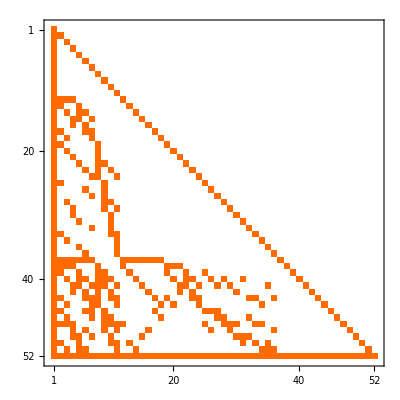

```mathematica
mat=Table[
FullBaseCoeff[allGraphs5[k,"colofour"]],
{k,theGens}
];MatrixPlot[mat]
```

```mathematica
mat2=Table[
FullBaseCoeff[allGraphs5[k,"colofour"]],
{k,Sort[allGraphs5NullAtomKeys,CompareSymbols[allGraphs5[#1,"colofourrealnull"],allGraphs5[#2,"colofourrealnull"]]&]}
];
```

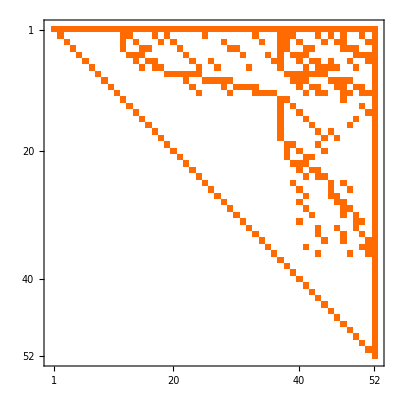

```mathematica
MatrixPlot[mat2]
```

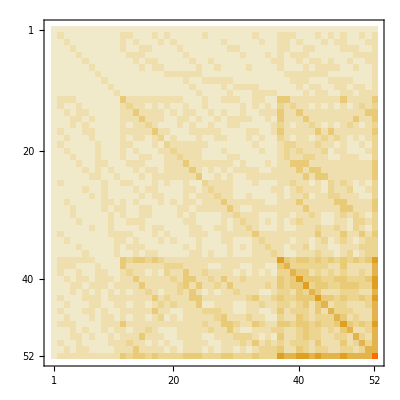

```mathematica
mat.mat2//MatrixPlot
```

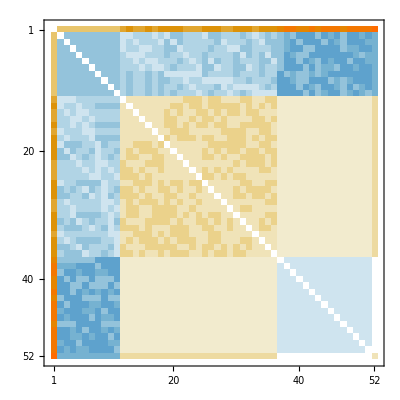

```mathematica
mat2.Inverse[mat]+Transpose[mat2.Inverse[mat]]//MatrixPlot
```

```mathematica
mat2.mat//MatrixForm
```

(52 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
15 | 15 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 2 | 2 | 2 | 5 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1
15 | 5 | 15 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 2 | 5 | 2 | 2 | 2 | 5 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1
15 | 5 | 5 | 15 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 2 | 2 | 5 | 5 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 1
15 | 5 | 5 | 5 | 15 | 5 | 5 | 5 | 5 | 5 | 5 | 2 | 5 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 5 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 1
15 | 5 | 5 | 5 | 5 | 15 | 5 | 5 | 5 | 5 | 5 | 2 | 2 | 5 | 2 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1
15 | 5 | 5 | 5 | 5 | 5 | 15 | 5 | 5 | 5 | 5 | 2 | 2 | 2 | 5 | 2 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 1
15 | 5 | 5 | 5 | 5 | 5 | 5 | 15 | 5 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 5 | 5 | 5 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
15 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 15 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 5 | 5 | 5 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1
15 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 15 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 5 | 2 | 5 | 5 | 5 | 5 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1
15 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 15 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 5 | 5 | 5 | 5 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 1
5 | 5 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1
5 | 5 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1
5 | 2 | 5 | 2 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1
5 | 2 | 2 | 5 | 5 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1
5 | 2 | 2 | 5 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1
5 | 5 | 2 | 2 | 2 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 5 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1
5 | 5 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 5 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 5 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 5 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 2 | 5 | 2 | 2 | 5 | 5 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 2 | 2 | 5 | 2 | 5 | 2 | 5 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 5 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 2 | 2 | 2 | 5 | 5 | 2 | 2 | 5 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 5 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 5 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 5 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1
5 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 5 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 5 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 5 | 5 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 5 | 2 | 5 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1
5 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1
5 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 5 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 5 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1
5 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 5 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 5 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1
5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 5 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1
5 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 5 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1
5 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 5 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 5 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1
5 | 2 | 2 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 5 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 5 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1
2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1
2 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1
2 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1
2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
mat==mat2
```

True

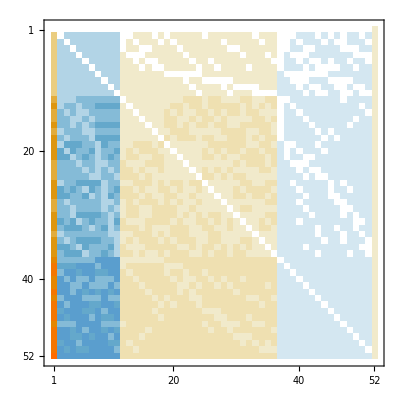

```mathematica
mat2=Table[
EmptyBaseCoeff[allGraphs5[k,"colofourrealnull"]],
{k,theGens}
];MatrixPlot[mat2//Inverse]
```

```mathematica
mat//Inverse//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 2 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | 2 | -6 | 2 | 2 | 2 | -1 | 2 | -1 | -1 | -1 | 2 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | -2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 2 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | 0 | -6 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1
0 | 0 | 0 | 0 | -6 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
0 | 0 | 0 | 0 | -2 | 2 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | -6 | 0 | 0 | 2 | 0 | 2 | 0 | -1 | 0 | 0 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 | 0 | 2 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 0 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 | 0 | 1 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2 | -6 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 2 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 | 1 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | 2 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 2 | -6 | 24 | -6 | -6 | -6 | 2 | -6 | 2 | 2 | 2 | -6 | 2 | 2 | -6 | 2 | 2 | 2 | -1 | -6 | 2 | 2 | 2 | -1 | 2 | -1 | 2 | -6 | 2 | 2 | -1 | 2 | -1 | 2 | -1 | -1 | -1 | 2 | -6 | 2 | 2 | 2 | -1 | 2 | -1 | -1 | -1 | 2 | -1 | -1)

```mathematica
ChangeSymbol
```

```mathematica
ChangeSymbol[s_,prefix_]:=Symbol[StringReplace[SymbolName[s],"n"->prefix]]
```

```mathematica
Reduce[
Table[
ChangeSymbol[First[allGraphs5[k,"generators"]],"g"]==allGraphs5[k,"colofour"],
{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&Length[ListofVars[allGraphs5[#,"generators"]]]==1&]}
],Map[allGraphs5[#,"colofour"]&,allGraphs5AtomKeys]
]
```

v1x2x3x4x5==g1x2x3x4x5&&v1x2x3x45==g1x2x3x45-g1x2x3x4x5&&v1x2x35x4==g1x2x35x4-g1x2x3x4x5&&v1x2x34x5==g1x2x34x5-g1x2x3x4x5&&v1x2x345==g1x2x345-g1x2x34x5-g1x2x35x4-g1x2x3x45+2 g1x2x3x4x5&&v1x25x3x4==g1x25x3x4-g1x2x3x4x5&&v1x25x34==g1x25x34-g1x25x3x4-g1x2x34x5+g1x2x3x4x5&&v1x24x3x5==g1x24x3x5-g1x2x3x4x5&&v1x24x35==g1x24x35-g1x24x3x5-g1x2x35x4+g1x2x3x4x5&&v1x245x3==g1x245x3-g1x24x3x5-g1x25x3x4-g1x2x3x45+2 g1x2x3x4x5&&v1x23x4x5==g1x23x4x5-g1x2x3x4x5&&v1x23x45==g1x23x45-g1x23x4x5-g1x2x3x45+g1x2x3x4x5&&v1x235x4==g1x235x4-g1x23x4x5-g1x25x3x4-g1x2x35x4+2 g1x2x3x4x5&&v1x234x5==g1x234x5-g1x23x4x5-g1x24x3x5-g1x2x34x5+2 g1x2x3x4x5&&v1x2345==g1x2345-g1x234x5-g1x235x4-g1x23x45+2 g1x23x4x5-g1x245x3-g1x24x35+2 g1x24x3x5-g1x25x34+2 g1x25x3x4-g1x2x345+2 g1x2x34x5+2 g1x2x35x4+2 g1x2x3x45-6 g1x2x3x4x5&&v15x2x3x4==g15x2x3x4-g1x2x3x4x5&&v15x2x34==g15x2x34-g15x2x3x4-g1x2x34x5+g1x2x3x4x5&&v15x24x3==g15x24x3-g15x2x3x4-g1x24x3x5+g1x2x3x4x5&&v15x23x4==g15x23x4-g15x2x3x4-g1x23x4x5+g1x2x3x4x5&&v15x234==g15x234-g15x23x4-g15x24x3-g15x2x34+2 g15x2x3x4-g1x234x5+g1x23x4x5+g1x24x3x5+g1x2x34x5-2 g1x2x3x4x5&&v14x2x3x5==g14x2x3x5-g1x2x3x4x5&&v14x2x35==g14x2x35-g14x2x3x5-g1x2x35x4+g1x2x3x4x5&&v14x25x3==g14x25x3-g14x2x3x5-g1x25x3x4+g1x2x3x4x5&&v14x23x5==g14x23x5-g14x2x3x5-g1x23x4x5+g1x2x3x4x5&&v14x235==g14x235-g14x23x5-g14x25x3-g14x2x35+2 g14x2x3x5-g1x235x4+g1x23x4x5+g1x25x3x4+g1x2x35x4-2 g1x2x3x4x5&&v145x2x3==g145x2x3-g14x2x3x5-g15x2x3x4-g1x2x3x45+2 g1x2x3x4x5&&v145x23==g145x23-g145x2x3-g14x23x5+g14x2x3x5-g15x23x4+g15x2x3x4-g1x23x45+2 g1x23x4x5+g1x2x3x45-2 g1x2x3x4x5&&v13x2x4x5==g13x2x4x5-g1x2x3x4x5&&v13x2x45==g13x2x45-g13x2x4x5-g1x2x3x45+g1x2x3x4x5&&v13x25x4==g13x25x4-g13x2x4x5-g1x25x3x4+g1x2x3x4x5&&v13x24x5==g13x24x5-g13x2x4x5-g1x24x3x5+g1x2x3x4x5&&v13x245==g13x245-g13x24x5-g13x25x4-g13x2x45+2 g13x2x4x5-g1x245x3+g1x24x3x5+g1x25x3x4+g1x2x3x45-2 g1x2x3x4x5&&v135x2x4==g135x2x4-g13x2x4x5-g15x2x3x4-g1x2x35x4+2 g1x2x3x4x5&&v135x24==g135x24-g135x2x4-g13x24x5+g13x2x4x5-g15x24x3+g15x2x3x4-g1x24x35+2 g1x24x3x5+g1x2x35x4-2 g1x2x3x4x5&&v134x2x5==g134x2x5-g13x2x4x5-g14x2x3x5-g1x2x34x5+2 g1x2x3x4x5&&v134x25==g134x25-g134x2x5-g13x25x4+g13x2x4x5-g14x25x3+g14x2x3x5-g1x25x34+2 g1x25x3x4+g1x2x34x5-2 g1x2x3x4x5&&v1345x2==g1345x2-g134x2x5-g135x2x4-g13x2x45+2 g13x2x4x5-g145x2x3-g14x2x35+2 g14x2x3x5-g15x2x34+2 g15x2x3x4-g1x2x345+2 g1x2x34x5+2 g1x2x35x4+2 g1x2x3x45-6 g1x2x3x4x5&&v12x3x4x5==g12x3x4x5-g1x2x3x4x5&&v12x3x45==g12x3x45-g12x3x4x5-g1x2x3x45+g1x2x3x4x5&&v12x35x4==g12x35x4-g12x3x4x5-g1x2x35x4+g1x2x3x4x5&&v12x34x5==g12x34x5-g12x3x4x5-g1x2x34x5+g1x2x3x4x5&&v12x345==g12x345-g12x34x5-g12x35x4-g12x3x45+2 g12x3x4x5-g1x2x345+g1x2x34x5+g1x2x35x4+g1x2x3x45-2 g1x2x3x4x5&&v125x3x4==g125x3x4-g12x3x4x5-g15x2x3x4-g1x25x3x4+2 g1x2x3x4x5&&v125x34==g125x34-g125x3x4-g12x34x5+g12x3x4x5-g15x2x34+g15x2x3x4-g1x25x34+g1x25x3x4+2 g1x2x34x5-2 g1x2x3x4x5&&v124x3x5==g124x3x5-g12x3x4x5-g14x2x3x5-g1x24x3x5+2 g1x2x3x4x5&&v124x35==g124x35-g124x3x5-g12x35x4+g12x3x4x5-g14x2x35+g14x2x3x5-g1x24x35+g1x24x3x5+2 g1x2x35x4-2 g1x2x3x4x5&&v1245x3==g1245x3-g124x3x5-g125x3x4-g12x3x45+2 g12x3x4x5-g145x2x3-g14x25x3+2 g14x2x3x5-g15x24x3+2 g15x2x3x4-g1x245x3+2 g1x24x3x5+2 g1x25x3x4+2 g1x2x3x45-6 g1x2x3x4x5&&v123x4x5==g123x4x5-g12x3x4x5-g13x2x4x5-g1x23x4x5+2 g1x2x3x4x5&&v123x45==g123x45-g123x4x5-g12x3x45+g12x3x4x5-g13x2x45+g13x2x4x5-g1x23x45+g1x23x4x5+2 g1x2x3x45-2 g1x2x3x4x5&&v1235x4==g1235x4-g123x4x5-g125x3x4-g12x35x4+2 g12x3x4x5-g135x2x4-g13x25x4+2 g13x2x4x5-g15x23x4+2 g15x2x3x4-g1x235x4+2 g1x23x4x5+2 g1x25x3x4+2 g1x2x35x4-6 g1x2x3x4x5&&v1234x5==g1234x5-g123x4x5-g124x3x5-g12x34x5+2 g12x3x4x5-g134x2x5-g13x24x5+2 g13x2x4x5-g14x23x5+2 g14x2x3x5-g1x234x5+2 g1x23x4x5+2 g1x24x3x5+2 g1x2x34x5-6 g1x2x3x4x5&&v12345==g12345-g1234x5-g1235x4-g123x45+2 g123x4x5-g1245x3-g124x35+2 g124x3x5-g125x34+2 g125x3x4-g12x345+2 g12x34x5+2 g12x35x4+2 g12x3x45-6 g12x3x4x5-g1345x2-g134x25+2 g134x2x5-g135x24+2 g135x2x4-g13x245+2 g13x24x5+2 g13x25x4+2 g13x2x45-6 g13x2x4x5-g145x23+2 g145x2x3-g14x235+2 g14x23x5+2 g14x25x3+2 g14x2x35-6 g14x2x3x5-g15x234+2 g15x23x4+2 g15x24x3+2 g15x2x34-6 g15x2x3x4-g1x2345+2 g1x234x5+2 g1x235x4+2 g1x23x45-6 g1x23x4x5+2 g1x245x3+2 g1x24x35-6 g1x24x3x5+2 g1x25x34-6 g1x25x3x4+2 g1x2x345-6 g1x2x34x5-6 g1x2x35x4-6 g1x2x3x45+24 g1x2x3x4x5

```mathematica
MatrixRank[mat]
```

52

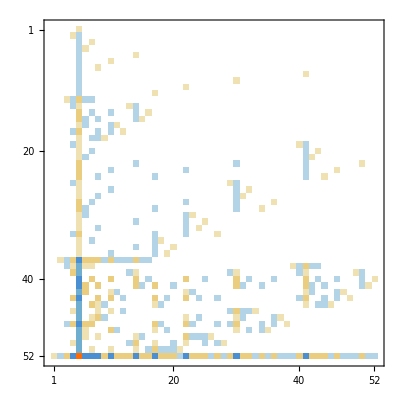

```mathematica
Inverse[mat]//MatrixPlot
```

```mathematica
Sort[Table[k,{k,Select[Keys[allGraphs5],allGraphs5[#,"generators"]==allGraphs5[0,"generators"]&]}]]==Sort[allGraphs5NullAtomKeys]
```

True

```mathematica
TableForm[
Sort[
Select[
Table[
{ShowGraph[allGraphs5,k],allGraphs5[k,"generators"],Length[ListofVars[allGraphs5[k,"colofour"]]],allGraphs5[k,"colofour"]},{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==1&]}],
Length[#[[2]]]==1&
],
#1[[3]]>#2[[3]]&
]
]
```

-Graphics-59048 | n12345 | 1 | v12345

```mathematica
FaceForm
```

```mathematica
Select[
```